# Lifetime metrology: probe optimisation

Dr Jesús Rubio
University of Surrey
j.rubiojimenez@surrey.ac.uk
ORCID iD: 0000-0002-8193-8273

Created: May 2024
Last update: July 2025

## Preamble: prior information, probe state, and symmetry function

```mathematica
Clear[θmin,θmax,a,p,ρ,η,f]
θmin=1/a;θmax=a;p=1/(θ Integrate[1/θ,{θ,θmin,θmax}]);
ρ={{η Exp[- 1/θ],Sqrt[η(1-η)] Exp[- 1/(2θ)]},{Sqrt[η(1-η)] Exp[- 1/(2θ)],1-η Exp[- 1/θ]}};
f[θ_]=Log[θ];
```

## Probe optimisation

### ρ_0, ρ_1 and S operators

```mathematica
Clear[temp0,temp1]
temp0[θ_]=Normal[Integrate[p ρ,θ]];temp1[θ_]=Normal[Integrate[p ρ f[θ],θ]];
```

```mathematica
Clear[ρ0 ,ρ1]
ρ0=temp0[θmax]-temp0[θmin];ρ1=temp1[θmax]-temp1[θmin];
```

```mathematica
Clear[S]
S=LyapunovSolve[ρ0,2ρ1];
```

### Absolute precision gain

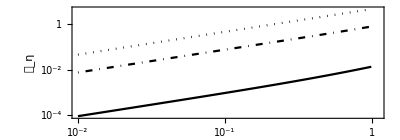

```mathematica
Clear[a,insetProbe]
insetProbe=LogLogPlot[{N[Tr[S.ρ1]]/.a->2,N[Tr[S.ρ1]]/.a->10,N[Tr[S.ρ1]]/.a->100},{η,0.01,0.99},FrameStyle->Directive["Times",13,Black],Frame->True,PlotStyle->{{Black},{DotDashed,Black},{Dotted,Black}},FrameLabel->{"η","𝒢_η"},AspectRatio->0.35,PlotRange->{{0,1.1},All},FrameTicks->{{{{0.0001,"10^-4"},{0.0002,""},{0.0003,""},{0.0004,""},{0.0005,""},{0.0006,""},{0.0007,""},{0.0008,""},{0.0009,""},{0.001,""},{0.002,""},{0.003,""},{0.004,""},{0.005,""},{0.006,""},{0.007,""},{0.008,""},{0.009,""},{0.01,"10^-2"},{0.02,""},{0.03,""},{0.04,""},{0.05,""},{0.06,""},{0.07,""},{0.08,""},{0.09,""},{0.1,""},{0.2,""},{0.3,""},{0.4,""},{0.5,""},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1,"1"},{1.1,""},{1.2,""},{1.3,""},{1.4,""},{1.5,""},{1.6,""},{1.7,""},{1.8,""}},None},{{{0.01,"10^-2"},{0.02,""},{0.03,""},{0.04,""},{0.05,""},{0.06,""},{0.07,""},{0.08,""},{0.09,""},{0.1,"10^-1"},{0.2,""},{0.3,""},{0.4,""},{0.5,""},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1,"1"}}, None}}]
```

## Protocol using the optimal probe state

### Optimal POM

```mathematica
Clear[a,η,aux1,s1ket,s2ket,optPOM1,optPOM2]
a=10;η=1; 
aux1=Eigenvectors[LyapunovSolve[ρ0,2ρ1]]; (* this instead of S to avoid numerical issues when η = 1 *)
s1ket=aux1[[1]]/Sqrt[aux1[[1]][[1]]^2+aux1[[1]][[2]]^2];
s2ket=aux1[[2]]/Sqrt[aux1[[2]][[1]]^2+aux1[[2]][[2]]^2];
optPOM1=KroneckerProduct[s1ket,s1ket];
optPOM2=KroneckerProduct[s2ket,s2ket];
Row[{MatrixForm[s1ket],",",MatrixForm[s2ket]}]
```

(1
0),(0
1)

### Minimum error for the given state

```mathematica
Clear[aux3,ϵprior,ϵMLE]
aux3=NIntegrate[p f[θ]^2,{θ,θmin,θmax}];
ϵprior = aux3-NIntegrate[p f[θ],{θ,θmin,θmax},AccuracyGoal->8]^2;
ϵMLE= aux3-Tr[ρ1.LyapunovSolve[ρ0,2ρ1]]
```

0.99018

## Protocol using a suboptimal probe state

### Optimal POM

```mathematica
Clear[ηsub,η,aux1sub,s1ketSub,s2ketSub,optPOM1sub,optPOM2sub]
ηsub=1./3;η=ηsub;
aux1sub=Eigenvectors[S];
s1ketSub=-aux1sub[[1]]/Sqrt[aux1sub[[1]][[1]]^2+aux1sub[[1]][[2]]^2];
s2ketSub=-aux1sub[[2]]/Sqrt[aux1sub[[2]][[1]]^2+aux1sub[[2]][[2]]^2];
optPOM1sub=KroneckerProduct[s1ketSub,s1ketSub];
optPOM2sub=KroneckerProduct[s2ketSub,s2ketSub];
Row[{MatrixForm[s1ketSub],",",MatrixForm[s2ketSub]}]
```

(0.899806
0.43629),(-0.43629
0.899806)

### Minimum error for the given state

```mathematica
Clear[aux3,ϵMLEsub]
aux3=NIntegrate[p f[θ]^2,{θ,θmin,θmax}];
ϵMLEsub=aux3-Tr[ρ1.LyapunovSolve[ρ0,2ρ1]]/.η->ηsub
Clear[η]
```

1.51888